# Lab: Linear Models with IVPs (Section 5.1)

## Background Equations

5.1.1 Spring/Mass systems: Free Undamped Motion

(d^2 x)/dt^2+ω^2 x=0		(1)
(ω^2=k/m)		


5.1.2: Spring/Mass Systems: Free Damped Motion

(d^2 x)/dt^2+2λ dx/dt+ω^2 x=0		(2)
(2λ=β/m,  ω^2=k/m)	
or
m(d^2 x)/dt^2+β dx/dt+k x=0                  (3)

## Part 1: Free Undamped Motion

(a) Use DSolve in Mathematica to verify the solution we found to (1).

```mathematica
DSolve[{x''[t]+ω^2 x[t] == 0},x[t],t]
```

{{x[t]→C[1] Cos[t ω]+C[2] Sin[t ω]}}

(b) A 4 ft spring measures 8 ft after a 8 lb mass is attached.  Find the equation of motion if the mass is released from equilibrium with downward velocity of 5 ft/s and there is no damping. (Remember that F=ks where s is displacement and F=ma.)

F = ks
8lb (Force) = k* displacement = k*4
k = 2lb/ft

F = ma
8 = m*32
1/4 = m

ω^2 = k/m= 2/(1/4)=8

(d^2 x)/dt^2+8x=0

x(0) = 0 (hasn’t moved at all- it’s a 4 ft spring, but it hasn’t moved at all the instant you put the weight on- 0, measure of displacement rather than position)
x’(0) = 5 (velocity)

```mathematica
DSolve[{x''[t]+8x[t]==0,x[0]==0,x'[0]==5},x[t],t]
```

{{x[t]→(5 Sin[2 √2 t])/(2 √2)}}

## Part 2: Free Damped Motion (Specific)

(a) Use DSolve in Mathematica to find a general solution to (2).
(d^2 x)/dt^2+2λ dx/dt+ω^2 x=0

```mathematica
DSolve[{x''[t]+2 λ x'[t] + ω x[t] ==0},x[t],t]
```

{{x[t]→ⅇ^(t (-λ-√(λ^2-ω))) C[1]+ⅇ^(t (-λ+√(λ^2-ω))) C[2]}}

How does this fit the form?

(b) A 4 ft spring measures 8 ft after a 8 lb mass is attached.  Find the equation of motion if the mass is released from equilibrium with downward velocity of 5 ft/s and damping is √2 times the instantaneous velocity.  (In other words, β=√2.) 

m (d^2 x)/dt^2+ B dx/dt+kx =0
? (d^2 x)/dt^2+ ? dx/dt+?x =0
1/4 (d^2 x)/dt^2+ √2 dx/dt+2x =0

x(0)=0
x’(0)=5
B = √2
2λ = B/m
m= 8/32
2λ = (√2)/(8/32)

```mathematica
Solve[2λ==(√2)/(8/32),λ]
```

{{λ→2 √2}}

F = ks
8lb (Force) = k* displacement = k*4
k = 2lb/ft

F = ma
8 = m*32
1/4 = m

ω^2 = k/m= 2/(1/4)=8
ω^2 = 8

```mathematica
DSolve[{x''[t]+4 √2 x'[t]+8 x[t]==0,x[0]==0,x'[0]==5},x[t],t]
```

{{x[t]→5 ⅇ^(-2 √2 t) t}}

## Part 3: Free Damped Motion (Extended)

(a) Plot both of your results from Part 1(b) and Part 2(b), explain the differences in the two graphs and describe the motion of the spring in each case.  Clearly label your graph.
We want to plot (5 Sin[2 √2 t])/(2 √2) and 5 ⅇ^(-2 √2 t) t.

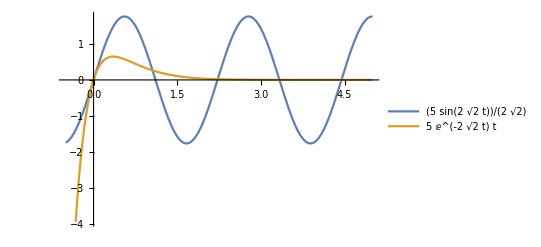

```mathematica
Plot[{(5 Sin[2 √2 t])/(2 √2),5 ⅇ^(-2 √2 t) t} ,{t,-.5,5},PlotLegends->"Expressions"]
```

a. (5 Sin[2 √2 t])/(2 √2) (The blue case) is underdamped.  We know this is obviously true because there is no damping (the damping is 0, which is smaller than the spring constant, k=2).

b. 5 ⅇ^(-2 √2 t) t (The orange case) 
λ = 2 √2
ω^2=8
λ^2= 8
λ^2-ω^2=0
Therefore, the situation is critically damped because λ^2-ω^2=0.

In the free damped situation, the system is said to be overdamped, critically damped, or underdamped in the following cases using the damped motion equation (2):

Case 1 (overdamped): λ^2-ω^2>0
The system is said to be overdamped because the damping coefficient β is large when compared to the spring constant k.

Case 2 (critically damped): λ^2-ω^2=0
The system is said to be critically damped because any slight decrease in the damping force would result in oscillatory motion.

Case 3 (underdamped): λ^2-ω^2<0
The system is said to be underdamped because the damping coefficient β is small in comparison to the spring constant k.

(b) Using your result from Part 2(a), explain how the three cases above result in characteristically different solutions.

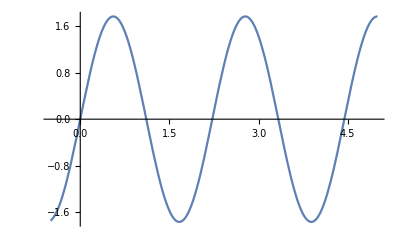

```mathematica
Plot[{(5 Sin[2 √2 t])/(2 √2)} ,{t,-.5,5},PlotLegends->"Expressions"]
```

The graph above is an example of an undamped case.  This spring will continue to move in a constant motion forever.

As a part of this explanation, create multiple, well labeled graphs that illustrate each of the three cases.  Use at least three curves (if not more) in each graph for each case.  (So you should have at least three graphs on each of three well-labeled plots/graphical images.)  Be clear with ANY values you are using.  If you use a problem from the book or the problems earlier in the lab as a starting point, say so and be clear with all steps.  Consider these graphs to be your explanation to a fellow undergraduate student of the differences in the cases.  Although you are creating graphs as a goal, you should have accompanying text that fully explains your process. Just because you have numbers in your Mathematica code (which I should see) you need to state all your choices.